## Scientific Programming 2

First steps in working with expressions

### Parts of expressions

```mathematica
(* Everything in Mathematica is an expression. 
Expressions have the form Head[e1,e2,...].
The simplest types of expressions are Integers, Reals, Rationals, Complex or List. 
*)
```

```mathematica
ls={a,b,c,d,e,f,g,h,i,j,k};
```

```mathematica
(* Mathematica lists are indexed beginning with 1. In C and other common programming languages, arrays are indexed starting with 0.
In Mathematica, the 0-th componenent of the list is reserved for the "head". The head gives much information about the type of expression in question. *)
```

```mathematica
ls⟦0⟧
```

List

```mathematica
Length[ls]
```

11

```mathematica
Part[ls,1]
```

a

```mathematica
ls⟦1⟧
```

a

```mathematica
?Part
```

RowBox[{StyleBox["expr", "TI"], "[", RowBox[{"[", StyleBox["i", "TI"], "]"}], "]"}] or RowBox[{"Part", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["i", "TI"]}], "]"}] gives the StyleBox["i", "TI"]SuperscriptBox["", "th"] part of StyleBox["expr", "TI"]. 
RowBox[{StyleBox["expr", "TI"], "[", RowBox[{"[", RowBox[{"-", StyleBox["i", "TI"]}], "]"}], "]"}] counts from the end. 
RowBox[{StyleBox["expr", "TI"], "[", RowBox[{"[", RowBox[{StyleBox["i", "TI"], ",", StyleBox["j", "TI"], ",", StyleBox["…", "TR"]}], "]"}], "]"}] or RowBox[{"Part", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["i", "TI"], ",", StyleBox["j", "TI"], ",", StyleBox["…", "TR"]}], "]"}] is equivalent to RowBox[{RowBox[{RowBox[{StyleBox["expr", "TI"], "[", RowBox[{"[", StyleBox["i", "TI"], "]"}], "]"}], "[", RowBox[{"[", StyleBox["j", "TI"], "]"}], "]"}], StyleBox["…", "TR"]}]. 
RowBox[{StyleBox["expr", "TI"], "[", RowBox[{"[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}], "]"}] gives a list of the parts SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], SubscriptBox[StyleBox["i", "TI"], StyleBox["2", "TR"]], … of StyleBox["expr", "TI"]. 
RowBox[{StyleBox["expr", "TI"], "[", RowBox[{"[", RowBox[{StyleBox["m", "TI"], ";;", StyleBox["n", "TI"]}], "]"}], "]"}] gives parts StyleBox["m", "TI"] through StyleBox["n", "TI"].
RowBox[{StyleBox["expr", "TI"], "[", RowBox[{"[", RowBox[{StyleBox["m", "TI"], ";;", StyleBox["n", "TI"], ";;", StyleBox["s", "TI"]}], "]"}], "]"}] gives parts StyleBox["m", "TI"] through StyleBox["n", "TI"] in steps of StyleBox["s", "TI"].
RowBox[{StyleBox["expr", "TI"], "[", RowBox[{"[", StyleBox["\"\!\(\*StyleBox[\"key\",\"TI\"]\)\"", ShowStringCharacters->True], "]"}], "]"}] gives the value associated with the key "
StyleBox["key", "TI"]" in an association StyleBox["expr", "TI"].
RowBox[{StyleBox["expr", "TI"], "[", RowBox[{"[", RowBox[{"Key", "[", StyleBox["k", "TI"], "]"}], "]"}], "]"}] gives the value associated with an arbitrary key StyleBox["k", "TI"] in the association StyleBox["expr", "TI"].

```mathematica
ls⟦2;;7⟧
```

{b,c,d,e,f,g}

```mathematica
ls⟦2;;8;;2⟧
```

{b,d,f,h}

```mathematica
ls⟦-1⟧
```

k

```mathematica
ls⟦-3⟧
```

i

```mathematica
First[ls]
```

a

```mathematica
Rest[ls]
```

{b,c,d,e,f,g,h,i,j,k}

```mathematica
Last[ls]
```

k

```mathematica
Take[ls,2;;8;;2]
```

{b,d,f,h}

```mathematica
Take[ls,5]
```

{a,b,c,d,e}

```mathematica
Take[ls,{5,7}]
```

{e,f,g}

```mathematica
Drop[ls,5]
```

{f,g,h,i,j,k}

```mathematica
ReplacePart[ls,3->x]
```

{a,b,x,d,e,f,g,h,i,j,k}

```mathematica
?ReplacePart
```

ReplacePart[expr,i→new] yields an expression in which the i^th part of expr is replaced by new. 
ReplacePart[expr,{i_1→new_1,i_2→new_2,…}] replaces parts at positions i_n by new_n. 
ReplacePart[expr,{i,j,…}→new] replaces the part at position {i,j,…}. 
ReplacePart[expr,{{i_1,j_1,…}→new_1,…}] replaces parts at positions {i_n,j_n,…} by new_n. 
ReplacePart[expr,{{i_1,j_1,…},…}→new] replaces all parts at positions {i_n,j_n,…} by new. 
ReplacePart[i→new] represents an operator form of ReplacePart that can be applied to an expression.

```mathematica
(* More complex expressions can be navigated through in the same way as lists. 
Expressions have several levels, the total number of which is given by Depth[expression]. 
At level 0, we find the Head.
*)
```

```mathematica
expr=a+f[x,y^n];
```

```mathematica
FullForm[expr]
```

Plus[a,f[x,Power[y,n]]]

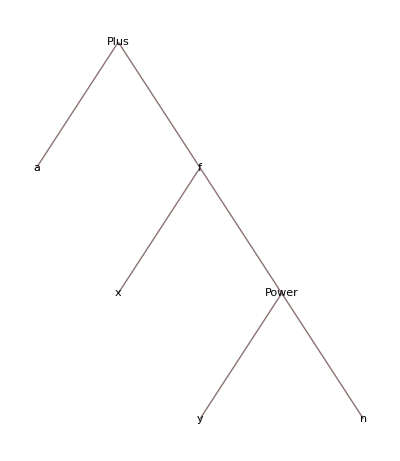

```mathematica
TreeForm[expr]
```

```mathematica
Depth[expr]
```

4

```mathematica
Level[expr,1]
```

{a,f[x,y^n]}

```mathematica
Level[expr,2]
```

{a,x,y^n,f[x,y^n]}

```mathematica
Level[expr,3]
```

{a,x,y,n,y^n,f[x,y^n]}

```mathematica
expr[[0]]
```

Plus

```mathematica
expr[[2,2,0]]
```

Power

```mathematica
ReplacePart[expr,{2,2,0}->Plus]
```

a+f[x,n+y]

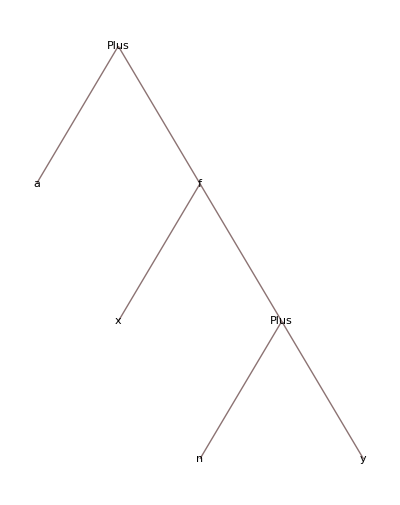

```mathematica
TreeForm[%]
```

### Pure Functions

```mathematica
Function[u,3+u][2]
Function[{x,y},x+y][{1,2},2]
```

5

{3,4}

```mathematica
Function[3+#][x]
Function[#1+#2][1,2]
```

3+x

3

```mathematica
g=(#+3)&;
g[x]
(#+3)&[x]
```

3+x

3+x

```mathematica
Context[Plus]
```

System`

```mathematica
?g
```

Global`g

g=#1+3&

```mathematica
FullForm[g]
```

Function[Plus[Slot[1],3]]

```mathematica
h=(#1+#2)&
h[1,2]
```

#1+#2&

3

```mathematica
?h
```

Global`h

h=#1+#2&

```mathematica
FullForm[h]
```

Function[Plus[Slot[1],Slot[2]]]

```mathematica
f[x_]:=x+3;
f[2]
```

5

```mathematica
Head[f]
```

Symbol

```mathematica
(* The expressions f and g can both be used as "functions". 
However, they are different. f is recognised by Mathematica as a Symbol, for which the rule f[x_]:=x+3 has been associated.
On the other hand, g is recognised a Function, i.e. a pure function. 
There are situations when a pure function is required, such as selecting parts of expressions with functions.
*)
```

```mathematica
Clear[f,g,h];
```

```mathematica
ls
```

{a,b,c,d,e,f,g,h,i,j,k}

```mathematica
Select[ls,(#==a)&]
```

{a}

### Map and Apply

```mathematica
ls
```

{a,b,c,d,e,f,g,h,i,j,k}

```mathematica
(* Map[F,expr] applies F to each element on the first level in expr *)
```

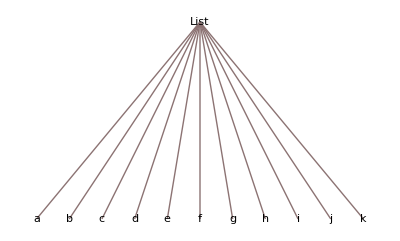

```mathematica
TreeForm[ls]
```

```mathematica
Map[F,ls]
```

{F[a],F[b],F[c],F[d],F[e],F[f],F[g],F[h],F[i],F[j],F[k]}

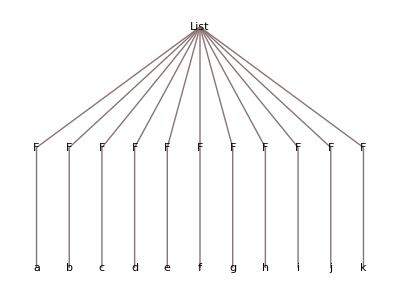

```mathematica
TreeForm[Map[F,ls]]
```

```mathematica
F/@ls
```

{F[a],F[b],F[c],F[d],F[e],F[f],F[g],F[h],F[i],F[j],F[k]}

```mathematica
F@x
```

F[x]

An expression does not have to be a list

```mathematica
g[a,b,c]//FullForm
```

g[a,b,c]

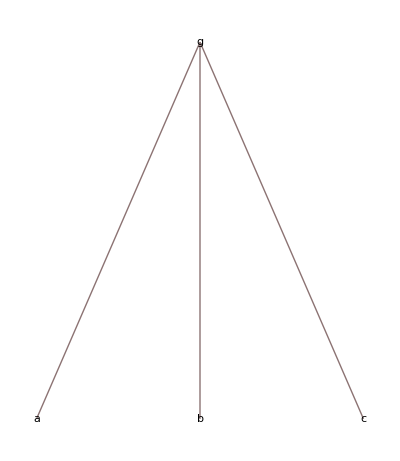

```mathematica
TreeForm[g[a,b,c]]
```

```mathematica
Head[%]
```

g

```mathematica
f/@g[a,b,c]
```

g[f[a],f[b],f[c]]

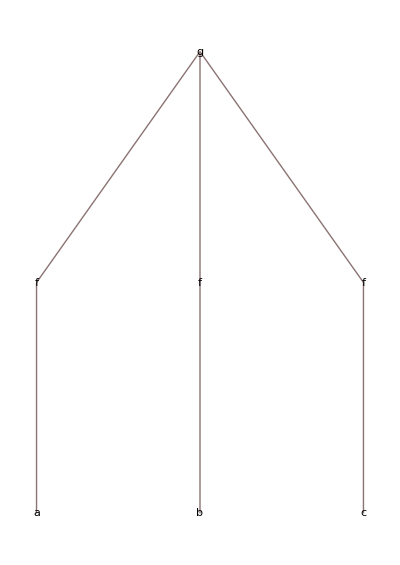

```mathematica
TreeForm[f/@g[a,b,c]]
```

Some functions are Listable

```mathematica
Log[x]
```

Log[x]

```mathematica
Log/@ls
```

{Log[a],Log[b],Log[c],Log[d],Log[e],Log[f],Log[g],Log[h],Log[i],Log[j],Log[k]}

```mathematica
Log[ls]
```

{Log[a],Log[b],Log[c],Log[d],Log[e],Log[f],Log[g],Log[h],Log[i],Log[j],Log[k]}

```mathematica
Attributes[Log]
```

{Listable,NumericFunction,Protected}

```mathematica
SetAttributes[h, Listable]
```

```mathematica
?h
```

Global`h

```mathematica
h[{a,b,c}]
```

{h[a],h[b],h[c]}

```mathematica
Clear[h]
```

```mathematica
?h
```

Global`h

Attributes[h]={Listable}

```mathematica
ClearAll[h]
```

```mathematica
?h
```

Global`h

```mathematica
Remove[h]
```

```mathematica
?h
```

Information::notfound: Symbol "h" not found.

Sin and Power, for example, have the attribute Listable

```mathematica
{a,b,c,d}^4
```

{a^4,b^4,c^4,d^4}

```mathematica
rlis=Table[RandomReal[{0,π}],{10^6}];
```

```mathematica
Take[rlis,10]
```

{2.31939,2.9894,0.251064,1.45485,1.06228,2.65924,0.245313,1.42109,2.48402,2.51624}

```mathematica
Timing[Sin/@rlis]⟦1⟧
```

0.06697

```mathematica
Timing[Sin[rlis]]⟦1⟧
```

0.01445

```mathematica
%%/%
```

4.634

Sometimes you want to Map to a particular part of an expression

```mathematica
?MapAt
```

RowBox[{"MapAt", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"], ",", StyleBox["n", "TI"]}], "]"}] applies StyleBox["f", "TI"] to the element at position StyleBox["n", "TI"] in StyleBox["expr", "TI"]. If StyleBox["n", "TI"] is negative, the position is counted from the end. 
RowBox[{"MapAt", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", StyleBox["j", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] applies StyleBox["f", "TI"] to the part of StyleBox["expr", "TI"] at position RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", StyleBox["j", "TI"], ",", StyleBox["…", "TR"]}], "}"}]. 
RowBox[{"MapAt", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["1", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] applies StyleBox["f", "TI"] to parts of StyleBox["expr", "TI"] at several positions. 
RowBox[{"MapAt", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["pos", "TI"]}], "]"}] represents an operator form of MapAt that can be applied to an expression.

```mathematica
Map[h,{a,b,c,d,e}]
```

{h[a],h[b],h[c],h[d],h[e]}

```mathematica
MapAt[h,{a,b,c,d,e},3]
```

{a,b,h[c],d,e}

```mathematica
MapAt[h,{a,b,c,d,e},1;;5;;2]
```

{h[a],b,h[c],d,h[e]}

```mathematica
(* Apply[f,expr] replaces the head of expr by f.*)
```

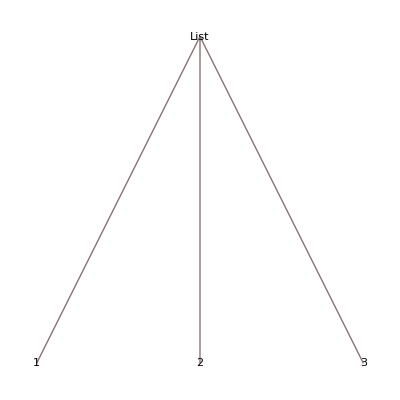

```mathematica
TreeForm[{1,2,3}]
```

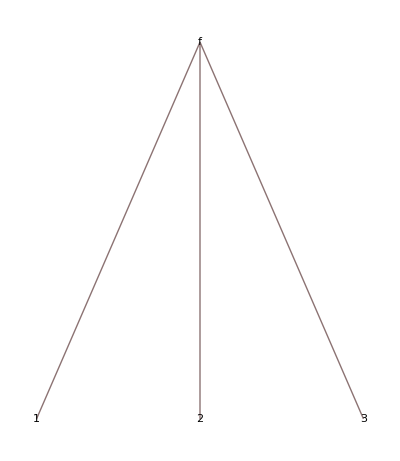

```mathematica
TreeForm[Apply[f,{1,2,3}]]
```

Apply changes the head of an expression

```mathematica
Head[{a,b,c,d}]
```

List

```mathematica
Apply[f,{a,b,c,d}]
```

f[a,b,c,d]

```mathematica
Head[%]
```

f

```mathematica
f@@{a,b,c,d}
```

f[a,b,c,d]

```mathematica
{a,b,c,d}//FullForm
```

List[a,b,c,d]

```mathematica
a+b+c+d//FullForm
```

Plus[a,b,c,d]

```mathematica
Plus@@{a,b,c,d}
```

a+b+c+d

```mathematica
Plus@@Map[f,{a,b,c,d}]
```

f[a]+f[b]+f[c]+f[d]

```mathematica
Clear[f]
```

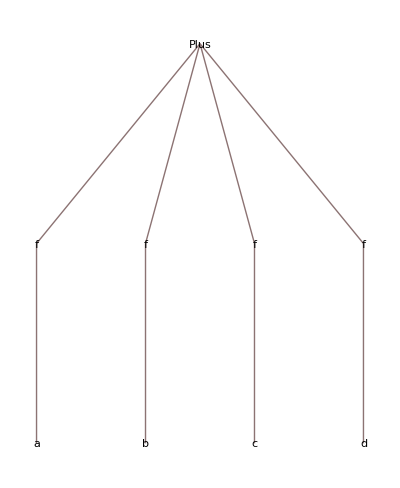

```mathematica
TreeForm[Plus@@Map[f,{a,b,c,d}]]
```

```mathematica
f/@(a+b+c+d)
```

f[a]+f[b]+f[c]+f[d]

### Rule and RuleDelayed, Replace and ReplaceRepeated

```mathematica
?Rule
```

lhs->rhs or lhs→rhs represents a rule that transforms lhs to rhs.

```mathematica
{a,b,c,d}/.a->b
```

{b,b,c,d}

```mathematica
{a,b,c,d}/.{a->b,b->c}
```

{b,c,c,d}

```mathematica
{a,b,c,d}//.{a->b,b->c}
```

{c,c,c,d}

```mathematica
{x,x,x,x}/.x->RandomReal[]
```

{0.899056,0.899056,0.899056,0.899056}

```mathematica
{x,x,x,x}/.x:>RandomReal[]
```

{0.660942,0.276831,0.0733017,0.303138}

```mathematica
(* The difference between Rule and RuleDelayed is similar to the difference between Set (=) and SetDelayed (:=).
In the non-delayed case, the rhs is evaluated first and only after that the attribution (replacement) is performed. 
In the delayed case, the attribution lhs:=rhs is done first, and the evaluation is performed only when a value for lhs is provided. 
*)
```

```mathematica
factorial1[1]=1;
factorial1[n_]=n factorial1[n-1]
factorial1[4]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

Hold[-1022+n]

24

```mathematica
factorial2[1]=1;
factorial2[n_]:=n factorial2[n-1];
factorial2[4]
```

24

### Patterns

```mathematica
?_
```

_ or Blank[] is a pattern object that can stand for any Wolfram Language expression. 
_h or Blank[h] can stand for any expression with head h.

```mathematica
Clear[f];

f[x_]:=x^3-1
```

```mathematica
{f[2],f[y]}
```

{7,-1+y^3}

A function defined only for integer arguments

```mathematica
g[k_Integer]:= Prime[k]
```

```mathematica
{g[2],g[π]}
```

{3,g[π]}

```mathematica
?Prime
```

Prime[n] gives the n^th prime number.

```mathematica
earth = AstronomicalData["Earth","Image"]
```

-Graphics-

```mathematica
Clear[ls];

ls={4,3.14,17,"天高皇帝远",π,earth};
```

```mathematica
ls
```

{4,3.14,17,天高皇帝远,π,-Graphics-}

```mathematica
Head/@ls
```

{Integer,Real,Integer,String,Symbol,Image}

```mathematica
?Select
```

Select[list,crit] picks out all elements e_i of list for which crit[e_i] is True. 
Select[list,crit,n] picks out the first n elements for which crit[e_i] is True. 
Select[crit] represents an operator form of Select that can be applied to an expression.

```mathematica
?Cases
```

Cases[{e_1,e_2,…},pattern] gives a list of the e_i that match the pattern. 
Cases[{e_1,…},pattern→rhs] gives a list of the values of rhs corresponding to the e_i that match the pattern. 
Cases[expr,pattern,levelspec] gives a list of all parts of expr on levels specified by levelspec that match the pattern. 
Cases[expr,pattern→rhs,levelspec] gives the values of rhs that match the pattern. 
Cases[expr,pattern,levelspec,n] gives the first n parts in expr that match the pattern. 
Cases[pattern] represents an operator form of Cases that can be applied to an expression.

```mathematica
Select
```

```mathematica
Cases[ls,_]
```

{4,3.14,17,天高皇帝远,π,-Graphics-}

```mathematica
Cases[ls,_Symbol]
```

{π}

```mathematica
Cases[ls,_Image]
```

{-Graphics-}

```mathematica
Cases[ls, _String]
```

{天高皇帝远}

```mathematica
Cases[ls,_Integer]
```

{4,17}

```mathematica
Cases[ls, _?PrimeQ]
```

{17}

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

All the squares less than 100

```mathematica
Cases[Range[100], _?(IntegerQ[ Sqrt[#]]&) ]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Select[Range[100], IntegerQ[ Sqrt[#]]&]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
22/7/.x_/y_-> {x,y}
```

22/7

```mathematica
(* The replacement didn't work, because 22/7 and x/y are expressions with different structures. *)
```

```mathematica
FullForm[x/y]
```

Times[x,Power[y,-1]]

```mathematica
FullForm[22/7]
```

Rational[22,7]

```mathematica
FullForm[Rational[x,y]]
```

Rational[x,y]

```mathematica
22/7/.Rational[x_,y_]-> {x,y}
```

{22,7}

```mathematica
2.34+2.09 ⅈ/.x_+ⅈ y_ -> {x,y}
```

2.34+2.09 ⅈ

```mathematica
FullForm[2.34+2.09 ⅈ]
```

Complex[2.34,2.09]

```mathematica
FullForm[x+ⅈ y]
```

Plus[x,Times[Complex[0,1],y]]

```mathematica
2.34+2.09 ⅈ/.Complex[x_,y_] -> {x,y}
```

{2.34,2.09}

```mathematica
2.34+2.09 ⅈ/.z_ -> {Re[z],Im[z]}
```

{2.34,2.09}

```mathematica
zsolns=NSolve[z^7-1==0]
```

{{z→-0.900969-0.433884 ⅈ},{z→-0.900969+0.433884 ⅈ},{z→-0.222521-0.974928 ⅈ},{z→-0.222521+0.974928 ⅈ},{z→0.62349-0.781831 ⅈ},{z→0.62349+0.781831 ⅈ},{z→1.}}

```mathematica
pts={Re[z],Im[z]}/.zsolns
```

{{-0.900969,-0.433884},{-0.900969,0.433884},{-0.222521,-0.974928},{-0.222521,0.974928},{0.62349,-0.781831},{0.62349,0.781831},{1.,0}}

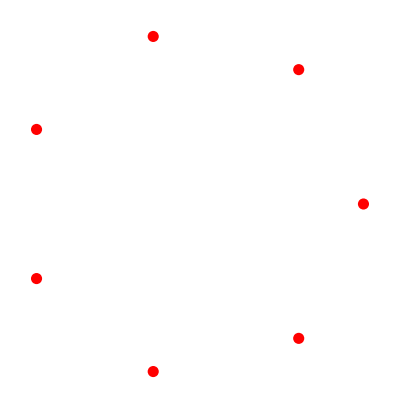

```mathematica
Graphics[{Red,AbsolutePointSize[8],Point[pts]},   
                    Axes-> Automatic]
```

Simple Programs

### Sieves

We want an efficient way of listing the primes up to some integer n. If we were willing to use the built in functions, and we wanted say the primes up to 100, we could proceed thus

```mathematica
?PrimePi
```

PrimePi[x] gives the number of primes π(x) less than or equal to x.

```mathematica
?Prime
```

Prime[n] gives the n^th prime number.

```mathematica
PrimePi[100]
```

25

```mathematica
Table[Prime[n],{n,1,25}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

or

```mathematica
Prime/@Range[25]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

Let us, however, proceed differently - write our own prime number list.

```mathematica
n=20;
```

```mathematica
Clear[lis];
lis=Range[n]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

First we remove the multiples of 2, apart from 2 itself:

```mathematica
k=2;
Do[lis⟦j⟧=1,{j,2k,n,k}] (*element 2k set to 1 and then in steps of size k, up to n*)
```

```mathematica
lis
```

{1,2,3,1,5,1,7,1,9,1,11,1,13,1,15,1,17,1,19,1}

```mathematica
?For
```

For[start,test,incr,body] executes start, then repeatedly evaluates body and incr until test fails to give True.

Now we remove, for each k≥2 all the remaining multiples of k, apart from k itself:

```mathematica
For[k=2,
    k≤ Floor[Sqrt[n]],
    k++,
    Do[ lis⟦i⟧=1,{i,2k,n,k}] ]; (*removes multiples of 2, then 3, then 4, then 5 which is already bigger than sqrt(n=20)*)
lis
```

{1,2,3,1,5,1,7,1,1,1,11,1,13,1,1,1,17,1,19,1}

```mathematica
DeleteCases[lis,1]
```

{2,3,5,7,11,13,17,19}

```mathematica
sieve[n_]:=
Module[{i,k,lis},
lis=Range[n];
For[k=2,
      k≤ Floor[Sqrt[n]],
      k++,
      Do[lis⟦i⟧=1,{i,2k,n,k}]];
DeleteCases[lis,1]
               ]
```

```mathematica
sieve[20]
```

{2,3,5,7,11,13,17,19}

```mathematica
Timing[sieve[1000]]
```

{0.,{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541,547,557,563,569,571,577,587,593,599,601,607,613,617,619,631,641,643,647,653,659,661,673,677,683,691,701,709,719,727,733,739,743,751,757,761,769,773,787,797,809,811,821,823,827,829,839,853,857,859,863,877,881,883,887,907,911,919,929,937,941,947,953,967,971,977,983,991,997}}

Once we have the sieve, we can define our own versions of Prime and PrimePi. We will need the function Position.

```mathematica
Position[{a,b,c,d,e},b]
```

{{2}}

```mathematica
Position[{a,b,c,b,b},b]
```

{{2},{4},{5}}

```mathematica
primetab=sieve[10^6];
```

Note the use of  = , rather than := , in the above.

```mathematica
Remove[primepi];
prime[n_]:=primetab⟦n⟧

primepi[x_]:=
Length[
Select[primetab,#≤x&]
	] (* # is a dummy and & terminates the function*)
```

```mathematica
prime[12]
```

37

```mathematica
primepi[37]
```

12

```mathematica
primepi[3584.5]
```

502

We can also make an attempt at NextPrime

```mathematica
nextprime[x_]:=prime[primepi[x] +1]
```

```mathematica
nextprime[x_,k_Integer]:=prime[primepi[x]+If[k>0,k,k+1]]/;k≠0
```

```mathematica
nextprime[137,1.5]
```

nextprime[137,1.5]

```mathematica
nextprime[137]
```

139

```mathematica
nextprime[138,-1]
```

137

```mathematica
nextprime[138,-2]
```

131

```mathematica
nextprime[131]
```

137

```mathematica
?nextprime
```

Global`nextprime

nextprime[x_]:=prime[primepi[x]+1]
 
nextprime[x_,k_Integer]:=prime[primepi[x]+If[k>0,k,k+1]]/;k≠0

```mathematica
Clear[nextprime]
```

```mathematica
nextprime[x_,k_Integer]:=prime[primepi[x]+If[k>0,k,k+1]]/;k≠0
```

```mathematica
nextprime[x_]:=nextprime[x,1];
```

```mathematica
?nextprime
```

Global`nextprime

nextprime[x_,k_Integer]:=prime[primepi[x]+If[k>0,k,k+1]]/;k≠0
 
nextprime[x_]:=nextprime[x,1]

```mathematica
nextprime[137]
```

139

### The Newton iteration again

We have a program based on iteration

```mathematica
root[init_,acc_]:=
Module[{x=init,y=init+1},
              While[Abs[x-y]>10^(-(acc+1)),
                         y=x;
                         x=N[x-f[x]/f'[x],acc+1]];
              x  ]
```

Nest is a function that maps a function repeatedly

```mathematica
Nest[g,x,4]
```

g[g[g[g[x]]]]

What we need is NestWhile

```mathematica
?NestWhile
```

RowBox[{"NestWhile", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"], ",", StyleBox["test", "TI"]}], "]"}] starts with StyleBox["expr", "TI"], then repeatedly applies StyleBox["f", "TI"] until applying StyleBox["test", "TI"] to the result no longer yields True. 
RowBox[{"NestWhile", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"], ",", StyleBox["test", "TI"], ",", StyleBox["m", "TI"]}], "]"}] supplies the most recent StyleBox["m", "TI"] results as arguments for StyleBox["test", "TI"] at each step. 
RowBox[{"NestWhile", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"], ",", StyleBox["test", "TI"], ",", "All"}], "]"}] supplies all results so far as arguments for StyleBox["test", "TI"] at each step. 
RowBox[{"NestWhile", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"], ",", StyleBox["test", "TI"], ",", StyleBox["m", "TI"], ",", StyleBox["max", "TI"]}], "]"}] applies StyleBox["f", "TI"] at most StyleBox["max", "TI"] times. 
RowBox[{"NestWhile", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"], ",", StyleBox["test", "TI"], ",", StyleBox["m", "TI"], ",", StyleBox["max", "TI"], ",", StyleBox["n", "TI"]}], "]"}] applies StyleBox["f", "TI"] an extra StyleBox["n", "TI"] times. 
RowBox[{"NestWhile", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"], ",", StyleBox["test", "TI"], ",", StyleBox["m", "TI"], ",", StyleBox["max", "TI"], ",", RowBox[{"-", StyleBox["n", "TI"]}]}], "]"}] returns the result found when StyleBox["f", "TI"] had been applied StyleBox["n", "TI"] fewer times.

```mathematica
Clear[f];

f[x_]:=x^2-2

update[{x_,y_},acc_]:={N[x-f[x]/f'[x],acc+1],x}
```

```mathematica
root1[init_,acc_]:=
NestWhile[update[#,acc]&,{init,init+1},Abs[#⟦1⟧-#⟦2⟧]>10^(-acc-1)&]⟦1⟧
```

```mathematica
root1[2,100]
```

1.4142135623730950488016887242096980785696718753769480731766797379907324784621070388503875343276416

Now we incorporate this in to a routine that finds a root of a general function.  We also introduce g[x] = ∂_x f[x], to avoid recomputing the derivative with each iteration.

```mathematica
findroot[fn_,init_, acc_]:=
Module[{x=init,y=init+1},
g[x_]:=fn'[x];
update[{x_,y_}]:={N[x-fn[x]/g[x],acc+5],x};
NestWhile[update[#]&,{init,init+1},Abs[#⟦1⟧-#⟦2⟧]>10^(-acc-5)&]⟦1⟧
              ]
```

```mathematica
f[x_]:=x^3-2
```

```mathematica
findroot[f,2,100]
```

1.25992104989487316476721060727822835057025146470150798008197511215529967651395948372939656243625509415

```mathematica
%^3-2
```

0.